```mathematica
RotationMatrix[phi0,{0,0,1}] .{Cos[Theta],Sin[Theta]*Cos[Phi],Sin[Theta]*Sin[Phi]}//MatrixForm
```

(Cos[phi0] Cos[Theta]-Cos[Phi] Sin[phi0] Sin[Theta]
Cos[Theta] Sin[phi0]+Cos[Phi] Cos[phi0] Sin[Theta]
Sin[Phi] Sin[Theta])

```mathematica
theta[Theta_,Phi_,phi0_]:=Module[{y=Cos[phi0] Cos[Theta]-Cos[Phi] Sin[phi0] Sin[Theta],x=Cos[Theta] Sin[phi0]+Cos[Phi] Cos[phi0] Sin[Theta],z=Sin[Phi] Sin[Theta]},
ArcTan[y,x]*0+1*ArcCos[z]
]
```

```mathematica
phi[Theta_,Phi_,phi0_]:=Module[{y=Cos[phi0] Cos[Theta]-Cos[Phi] Sin[phi0] Sin[Theta],x=Cos[Theta] Sin[phi0]+Cos[Phi] Cos[phi0] Sin[Theta],z=Sin[Phi] Sin[Theta]},
ArcTan[y,x]*1+0*ArcCos[z]
]
```

```mathematica
FullSimplify[D[theta[Theta,Phi,phi0],Theta]*D[phi[Theta,Phi,phi0],Phi]-D[theta[Theta,Phi,phi0],Phi]*D[phi[Theta,Phi,phi0],Theta]]
```

Piecewise[{{((Cos[Phi]^2+Cos[Theta]^2 Sin[Phi]^2) (Cos[Theta] Cot[Theta]+Cos[Phi]^2 Sin[Theta]))/((Cos[Phi]^2+Cot[Theta]^2) (Cos[Theta]^2+Cos[Phi]^2 Sin[Theta]^2)^(3/2)), Cos[Theta] Sin[phi0]+Cos[Phi] Cos[phi0] Sin[Theta]≠0}, {0, True}}]

```mathematica
FullSimplify[D[phi[Theta,Phi,phi0],Phi]]
```

1/(Cot[Theta] Csc[Phi]+Cos[Phi] Cot[Phi] Tan[Theta])

```mathematica
pHP[theta_,phi_,phi0_]:=1/4*(1-Cos[2*phi0])*(1+Sin[theta]^2*Cos[2*phi0])^(3/2)/(Pi*(1-Sin[theta]^2*Cos[2*phi0]*Cos[2*phi-2*phi0])^2)
```

```mathematica
Gam=16
```

16

```mathematica
Limit[pHP[theta,phi,phi0],phi0->Pi/4]
```

1/(4 π)

```mathematica
NIntegrate[pHP[theta[Theta,Phi,-ArcTan[8/Gam]/2],phi[Theta,Phi,-ArcTan[8/Gam]/2],ArcTan[8/Gam]/2]*((-2 Sin[Theta])/(√(3+Cos[2 Theta]+2 Cos[2 Phi] Sin[Theta]^2)))*Sin[theta[Theta,Phi,-ArcTan[8/Gam]/2]],{Phi,0,2*Pi},{Theta,0,Pi},WorkingPrecision->16 , Method->"GlobalAdaptive"]
```

-1.000000011152471

```mathematica
points=Table[{Phi,pHP[theta[Pi/6,Phi,ArcTan[8/Gam]/2],phi[Pi/6,Phi,ArcTan[8/Gam]/2],ArcTan[8/Gam]/2]},{Phi,Range[0,2*Pi,0.01]}]
```

{{0.,0.0716877},{0.01,0.0716922},{0.02,0.0717058},{0.03,0.0717284},{0.04,0.0717602},{0.05,0.071801},{0.06,0.0718509},{0.07,0.0719099},{0.08,0.071978},{0.09,0.0720553},{0.1,0.0721417},{0.11,0.0722373},{0.12,0.0723421},{0.13,0.0724562},{0.14,0.0725795},{0.15,0.0727121},{0.16,0.0728541},{0.17,0.0730054},{0.18,0.0731662},{0.19,0.0733363},{0.2,0.073516},{0.21,0.0737052},{0.22,0.073904},{0.23,0.0741125},{0.24,0.0743306},{0.25,0.0745585},{0.26,0.0747962},{0.27,0.0750438},{0.28,0.0753012},{0.29,0.0755687},{0.3,0.0758462},{0.31,0.0761338},{0.32,0.0764316},{0.33,0.0767396},{0.34,0.077058},{0.35,0.0773867},{0.36,0.0777259},{0.37,0.0780757},{0.38,0.078436},{0.39,0.078807},{0.4,0.0791888},{0.41,0.0795815},{0.42,0.079985},{0.43,0.0803995},{0.44,0.0808252},{0.45,0.0812619},{0.46,0.08171},{0.47,0.0821693},{0.48,0.08264},{0.49,0.0831222},{0.5,0.0836159},{0.51,0.0841213},{0.52,0.0846383},{0.53,0.0851671},{0.54,0.0857078},{0.55,0.0862604},{0.56,0.086825},{0.57,0.0874016},{0.58,0.0879903},{0.59,0.0885912},{0.6,0.0892043},{0.61,0.0898297},{0.62,0.0904675},{0.63,0.0911176},{0.64,0.0917801},{0.65,0.0924551},{0.66,0.0931426},{0.67,0.0938425},{0.68,0.094555},{0.69,0.09528},{0.7,0.0960175},{0.71,0.0967675},{0.72,0.0975301},{0.73,0.0983051},{0.74,0.0990925},{0.75,0.0998924},{0.76,0.100705},{0.77,0.101529},{0.78,0.102366},{0.79,0.103215},{0.8,0.104075},{0.81,0.104948},{0.82,0.105833},{0.83,0.106729},{0.84,0.107636},{0.85,0.108555},{0.86,0.109485},{0.87,0.110426},{0.88,0.111377},{0.89,0.112339},{0.9,0.113311},{0.91,0.114292},{0.92,0.115284},{0.93,0.116284},{0.94,0.117293},{0.95,0.118311},{0.96,0.119337},{0.97,0.12037},{0.98,0.12141},{0.99,0.122458},{1.,0.123511},{1.01,0.12457},{1.02,0.125634},{1.03,0.126703},{1.04,0.127776},{1.05,0.128852},{1.06,0.12993},{1.07,0.131011},{1.08,0.132093},{1.09,0.133175},{1.1,0.134257},{1.11,0.135338},{1.12,0.136418},{1.13,0.137494},{1.14,0.138567},{1.15,0.139636},{1.16,0.140699},{1.17,0.141756},{1.18,0.142806},{1.19,0.143848},{1.2,0.14488},{1.21,0.145903},{1.22,0.146914},{1.23,0.147913},{1.24,0.148898},{1.25,0.14987},{1.26,0.150826},{1.27,0.151765},{1.28,0.152687},{1.29,0.15359},{1.3,0.154474},{1.31,0.155336},{1.32,0.156177},{1.33,0.156996},{1.34,0.15779},{1.35,0.158559},{1.36,0.159302},{1.37,0.160019},{1.38,0.160707},{1.39,0.161366},{1.4,0.161996},{1.41,0.162595},{1.42,0.163163},{1.43,0.163698},{1.44,0.1642},{1.45,0.164668},{1.46,0.165102},{1.47,0.165501},{1.48,0.165863},{1.49,0.16619},{1.5,0.166479},{1.51,0.166731},{1.52,0.166946},{1.53,0.167123},{1.54,0.167261},{1.55,0.167361},{1.56,0.167422},{1.57,0.167444},{1.58,0.167428},{1.59,0.167373},{1.6,0.167279},{1.61,0.167147},{1.62,0.166977},{1.63,0.166768},{1.64,0.166522},{1.65,0.166238},{1.66,0.165918},{1.67,0.165561},{1.68,0.165168},{1.69,0.16474},{1.7,0.164277},{1.71,0.16378},{1.72,0.16325},{1.73,0.162688},{1.74,0.162094},{1.75,0.161469},{1.76,0.160814},{1.77,0.16013},{1.78,0.159418},{1.79,0.158679},{1.8,0.157914},{1.81,0.157124},{1.82,0.156309},{1.83,0.155472},{1.84,0.154613},{1.85,0.153732},{1.86,0.152832},{1.87,0.151913},{1.88,0.150976},{1.89,0.150023},{1.9,0.149054},{1.91,0.148071},{1.92,0.147074},{1.93,0.146065},{1.94,0.145044},{1.95,0.144013},{1.96,0.142973},{1.97,0.141924},{1.98,0.140868},{1.99,0.139806},{2.,0.138738},{2.01,0.137665},{2.02,0.136589},{2.03,0.13551},{2.04,0.134429},{2.05,0.133347},{2.06,0.132265},{2.07,0.131183},{2.08,0.130102},{2.09,0.129023},{2.1,0.127947},{2.11,0.126873},{2.12,0.125804},{2.13,0.124739},{2.14,0.123679},{2.15,0.122625},{2.16,0.121577},{2.17,0.120535},{2.18,0.119501},{2.19,0.118474},{2.2,0.117455},{2.21,0.116444},{2.22,0.115442},{2.23,0.11445},{2.24,0.113466},{2.25,0.112493},{2.26,0.111529},{2.27,0.110576},{2.28,0.109634},{2.29,0.108702},{2.3,0.107782},{2.31,0.106872},{2.32,0.105974},{2.33,0.105088},{2.34,0.104214},{2.35,0.103351},{2.36,0.1025},{2.37,0.101662},{2.38,0.100835},{2.39,0.100021},{2.4,0.0992191},{2.41,0.0984297},{2.42,0.0976527},{2.43,0.0968881},{2.44,0.0961361},{2.45,0.0953966},{2.46,0.0946696},{2.47,0.0939552},{2.48,0.0932532},{2.49,0.0925638},{2.5,0.0918868},{2.51,0.0912223},{2.52,0.0905702},{2.53,0.0899305},{2.54,0.0893031},{2.55,0.088688},{2.56,0.0880852},{2.57,0.0874945},{2.58,0.086916},{2.59,0.0863495},{2.6,0.085795},{2.61,0.0852524},{2.62,0.0847217},{2.63,0.0842028},{2.64,0.0836956},{2.65,0.0832},{2.66,0.082716},{2.67,0.0822435},{2.68,0.0817823},{2.69,0.0813325},{2.7,0.080894},{2.71,0.0804666},{2.72,0.0800503},{2.73,0.079645},{2.74,0.0792506},{2.75,0.0788671},{2.76,0.0784944},{2.77,0.0781323},{2.78,0.0777809},{2.79,0.07744},{2.8,0.0771096},{2.81,0.0767896},{2.82,0.07648},{2.83,0.0761805},{2.84,0.0758913},{2.85,0.0756122},{2.86,0.0753432},{2.87,0.0750841},{2.88,0.074835},{2.89,0.0745957},{2.9,0.0743663},{2.91,0.0741466},{2.92,0.0739366},{2.93,0.0737363},{2.94,0.0735455},{2.95,0.0733643},{2.96,0.0731926},{2.97,0.0730304},{2.98,0.0728776},{2.99,0.0727341},{3.,0.0726},{3.01,0.0724752},{3.02,0.0723597},{3.03,0.0722534},{3.04,0.0721563},{3.05,0.0720684},{3.06,0.0719897},{3.07,0.0719201},{3.08,0.0718597},{3.09,0.0718083},{3.1,0.0717661},{3.11,0.0717329},{3.12,0.0717088},{3.13,0.0716937},{3.14,0.0716878},{3.15,0.0716909},{3.16,0.071703},{3.17,0.0717242},{3.18,0.0717545},{3.19,0.0717939},{3.2,0.0718423},{3.21,0.0718999},{3.22,0.0719666},{3.23,0.0720424},{3.24,0.0721273},{3.25,0.0722215},{3.26,0.0723248},{3.27,0.0724374},{3.28,0.0725593},{3.29,0.0726904},{3.3,0.0728309},{3.31,0.0729807},{3.32,0.0731399},{3.33,0.0733086},{3.34,0.0734868},{3.35,0.0736745},{3.36,0.0738717},{3.37,0.0740787},{3.38,0.0742952},{3.39,0.0745216},{3.4,0.0747577},{3.41,0.0750037},{3.42,0.0752596},{3.43,0.0755254},{3.44,0.0758013},{3.45,0.0760873},{3.46,0.0763835},{3.47,0.0766899},{3.48,0.0770066},{3.49,0.0773337},{3.5,0.0776712},{3.51,0.0780192},{3.52,0.0783779},{3.53,0.0787472},{3.54,0.0791273},{3.55,0.0795182},{3.56,0.07992},{3.57,0.0803328},{3.58,0.0807566},{3.59,0.0811916},{3.6,0.0816378},{3.61,0.0820954},{3.62,0.0825643},{3.63,0.0830446},{3.64,0.0835365},{3.65,0.08404},{3.66,0.0845552},{3.67,0.0850821},{3.68,0.0856209},{3.69,0.0861716},{3.7,0.0867342},{3.71,0.0873089},{3.72,0.0878957},{3.73,0.0884947},{3.74,0.0891059},{3.75,0.0897293},{3.76,0.0903651},{3.77,0.0910132},{3.78,0.0916738},{3.79,0.0923468},{3.8,0.0930322},{3.81,0.0937302},{3.82,0.0944407},{3.83,0.0951637},{3.84,0.0958992},{3.85,0.0966472},{3.86,0.0974078},{3.87,0.0981808},{3.88,0.0989663},{3.89,0.0997642},{3.9,0.100574},{3.91,0.101397},{3.92,0.102232},{3.93,0.103079},{3.94,0.103937},{3.95,0.104808},{3.96,0.105691},{3.97,0.106585},{3.98,0.107491},{3.99,0.108408},{4.,0.109336},{4.01,0.110275},{4.02,0.111225},{4.03,0.112185},{4.04,0.113155},{4.05,0.114135},{4.06,0.115125},{4.07,0.116124},{4.08,0.117132},{4.09,0.118148},{4.1,0.119173},{4.11,0.120205},{4.12,0.121244},{4.13,0.12229},{4.14,0.123343},{4.15,0.124401},{4.16,0.125464},{4.17,0.126532},{4.18,0.127604},{4.19,0.12868},{4.2,0.129758},{4.21,0.130839},{4.22,0.13192},{4.23,0.133003},{4.24,0.134085},{4.25,0.135166},{4.26,0.136246},{4.27,0.137323},{4.28,0.138397},{4.29,0.139466},{4.3,0.14053},{4.31,0.141589},{4.32,0.14264},{4.33,0.143683},{4.34,0.144717},{4.35,0.145741},{4.36,0.146754},{4.37,0.147755},{4.38,0.148742},{4.39,0.149716},{4.4,0.150674},{4.41,0.151617},{4.42,0.152541},{4.43,0.153448},{4.44,0.154334},{4.45,0.155201},{4.46,0.156045},{4.47,0.156867},{4.48,0.157665},{4.49,0.158438},{4.5,0.159186},{4.51,0.159906},{4.52,0.160599},{4.53,0.161263},{4.54,0.161898},{4.55,0.162502},{4.56,0.163075},{4.57,0.163615},{4.58,0.164122},{4.59,0.164596},{4.6,0.165035},{4.61,0.165439},{4.62,0.165808},{4.63,0.16614},{4.64,0.166436},{4.65,0.166694},{4.66,0.166914},{4.67,0.167097},{4.68,0.167241},{4.69,0.167347},{4.7,0.167415},{4.71,0.167443},{4.72,0.167433},{4.73,0.167384},{4.74,0.167297},{4.75,0.167171},{4.76,0.167006},{4.77,0.166804},{4.78,0.166564},{4.79,0.166286},{4.8,0.165971},{4.81,0.16562},{4.82,0.165233},{4.83,0.16481},{4.84,0.164353},{4.85,0.163862},{4.86,0.163337},{4.87,0.16278},{4.88,0.16219},{4.89,0.16157},{4.9,0.16092},{4.91,0.160241},{4.92,0.159533},{4.93,0.158799},{4.94,0.158038},{4.95,0.157251},{4.96,0.156441},{4.97,0.155607},{4.98,0.154751},{4.99,0.153874},{5.,0.152977},{5.01,0.152061},{5.02,0.151127},{5.03,0.150176},{5.04,0.149209},{5.05,0.148228},{5.06,0.147233},{5.07,0.146226},{5.08,0.145207},{5.09,0.144178},{5.1,0.143139},{5.11,0.142092},{5.12,0.141037},{5.13,0.139975},{5.14,0.138908},{5.15,0.137837},{5.16,0.136761},{5.17,0.135682},{5.18,0.134602},{5.19,0.13352},{5.2,0.132437},{5.21,0.131355},{5.22,0.130274},{5.23,0.129195},{5.24,0.128118},{5.25,0.127044},{5.26,0.125974},{5.27,0.124908},{5.28,0.123848},{5.29,0.122792},{5.3,0.121743},{5.31,0.120701},{5.32,0.119665},{5.33,0.118637},{5.34,0.117616},{5.35,0.116604},{5.36,0.115601},{5.37,0.114607},{5.38,0.113622},{5.39,0.112647},{5.4,0.111682},{5.41,0.110728},{5.42,0.109783},{5.43,0.10885},{5.44,0.107928},{5.45,0.107016},{5.46,0.106117},{5.47,0.105229},{5.48,0.104352},{5.49,0.103487},{5.5,0.102635},{5.51,0.101794},{5.52,0.100966},{5.53,0.10015},{5.54,0.099346},{5.55,0.0985546},{5.56,0.0977756},{5.57,0.0970091},{5.58,0.096255},{5.59,0.0955135},{5.6,0.0947846},{5.61,0.0940681},{5.62,0.0933642},{5.63,0.0926727},{5.64,0.0919938},{5.65,0.0913273},{5.66,0.0906732},{5.67,0.0900315},{5.68,0.0894022},{5.69,0.0887852},{5.7,0.0881804},{5.71,0.0875878},{5.72,0.0870073},{5.73,0.0864389},{5.74,0.0858825},{5.75,0.0853381},{5.76,0.0848055},{5.77,0.0842847},{5.78,0.0837756},{5.79,0.0832782},{5.8,0.0827923},{5.81,0.082318},{5.82,0.081855},{5.83,0.0814034},{5.84,0.0809631},{5.85,0.0805339},{5.86,0.0801158},{5.87,0.0797088},{5.88,0.0793127},{5.89,0.0789275},{5.9,0.078553},{5.91,0.0781893},{5.92,0.0778362},{5.93,0.0774936},{5.94,0.0771616},{5.95,0.0768399},{5.96,0.0765286},{5.97,0.0762275},{5.98,0.0759367},{5.99,0.075656},{6.,0.0753853},{6.01,0.0751247},{6.02,0.074874},{6.03,0.0746332},{6.04,0.0744022},{6.05,0.0741809},{6.06,0.0739694},{6.07,0.0737675},{6.08,0.0735753},{6.09,0.0733925},{6.1,0.0732193},{6.11,0.0730556},{6.12,0.0729013},{6.13,0.0727563},{6.14,0.0726208},{6.15,0.0724945},{6.16,0.0723775},{6.17,0.0722697},{6.18,0.0721712},{6.19,0.0720818},{6.2,0.0720016},{6.21,0.0719306},{6.22,0.0718687},{6.23,0.0718159},{6.24,0.0717722},{6.25,0.0717376},{6.26,0.071712},{6.27,0.0716955},{6.28,0.0716881}}

```mathematica
Export["c:/temp/pHPphi.csv",points]
```

c:/temp/pHPphi.csv

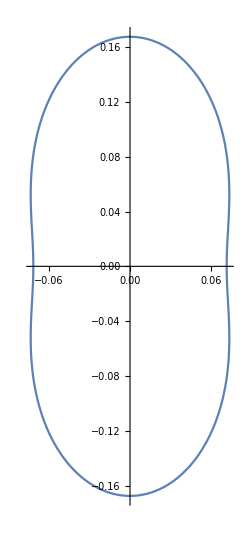

```mathematica
PolarPlot[pHP[theta[Pi/6,Phi,ArcTan[8/Gam]/2],phi[Pi/6,Phi,ArcTan[8/Gam]/2],ArcTan[8/Gam]/2] ,{Phi,0,2*Pi}]
```

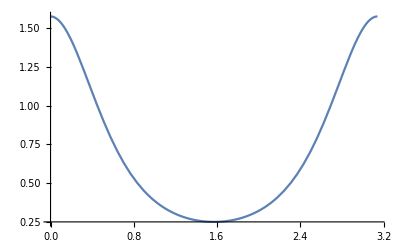

```mathematica
Plot[NIntegrate[pHP[theta[Theta,Phi,ArcTan[8/Gam]/2],phi[Theta,Phi,ArcTan[8/Gam]/2],ArcTan[8/Gam]/2],{Phi,0,2*Pi},WorkingPrecision->16 , Method->"GlobalAdaptive"] ,{Theta,0,Pi}]
```

```mathematica
FindRoot[NIntegrate[pHP[theta[Theta,Phi,ArcTan[8/Gamm]/2],phi[Theta,Phi,ArcTan[8/Gamm]/2],ArcTan[8/Gamm]/2]*Sin[Theta]*0.5*(3*Cos[Theta]^2-1),{Phi,0,2*Pi},{Theta,0,Pi}]-0.6,{Gamm,10}]
```

NIntegrate::inumr: The integrand (0.0397887 (1-1/(√(1+64/Gamm^2))) (-1+3 Cos[Theta]^2) Sin[Theta] (1+(1-Sin[«1»]^2 Sin[«1»]^2)/(√(1+64 Power[«2»])))^(3/2))/((1-(Cos[ArcTan[Times[«2»]]-2 ArcTan[«2»]] (1-Sin[«1»]^2 («1»)^2))/(√(1+64 Power[«2»])))^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159}}.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{Gamm→10.933}

```mathematica
points=Table[{Phi,pHP[theta[Pi/6,Phi,ArcTan[8/Gam]/2],phi[Pi/6,Phi,ArcTan[8/Gam]/2],ArcTan[8/Gam]/2]},{Phi,Range[0,2*Pi,0.01]}]
```

```mathematica
N[ArcTan[8/Gam]/2]
```

0.0322134

```mathematica
S2points=Table[{S2,FindRoot[NIntegrate[pHP[theta[Theta,Phi,ArcTan[8/Abs[Gamm]]/2],phi[Theta,Phi,ArcTan[8/Abs[Gamm]]/2],ArcTan[8/Abs[Gamm]]/2]*Sin[Theta]*0.5*(3*Cos[Theta]^2-1),{Phi,0,2*Pi},{Theta,0,Pi}]-S2,{Gamm,10^(-8),100}]},{S2,Range[0.01,0.95,0.01]}]
```

NIntegrate::inumr: The integrand (0.0397887 (1-1/(√(1+64/Abs[«1»]^2))) (-1+3 Cos[Theta]^2) Sin[Theta] (1+(1-Sin[«1»]^2 Sin[«1»]^2)/(√(1+64 Power[«2»])))^(3/2))/((1-(Cos[ArcTan[Times[«2»]]-2 ArcTan[«2»]] (1-Sin[«1»]^2 («1»)^2))/(√(1+64 Power[«2»])))^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.01,{Gamm→0.159028}},{0.02,{Gamm→0.316242}},{0.03,{Gamm→0.471829}},{0.04,{Gamm→0.625962}},{0.05,{Gamm→0.778806}},{0.06,{Gamm→0.930518}},{0.07,{Gamm→1.08124}},{0.08,{Gamm→1.23112}},{0.09,{Gamm→1.38029}},{0.1,{Gamm→1.52888}},{0.11,{Gamm→1.67701}},{0.12,{Gamm→1.8248}},{0.13,{Gamm→1.97237}},{0.14,{Gamm→2.11983}},{0.15,{Gamm→2.2673}},{0.16,{Gamm→2.41487}},{0.17,{Gamm→2.56266}},{0.18,{Gamm→2.71077}},{0.19,{Gamm→2.8593}},{0.2,{Gamm→3.00837}},{0.21,{Gamm→3.15806}},{0.22,{Gamm→3.3085}},{0.23,{Gamm→3.45977}},{0.24,{Gamm→3.61198}},{0.25,{Gamm→3.76525}},{0.26,{Gamm→3.91967}},{0.27,{Gamm→4.07535}},{0.28,{Gamm→4.23241}},{0.29,{Gamm→4.39095}},{0.3,{Gamm→4.5511}},{0.31,{Gamm→4.71297}},{0.32,{Gamm→4.87669}},{0.33,{Gamm→5.04237}},{0.34,{Gamm→5.21016}},{0.35,{Gamm→5.38018}},{0.36,{Gamm→5.55258}},{0.37,{Gamm→5.7275}},{0.38,{Gamm→5.9051}},{0.39,{Gamm→6.08553}},{0.4,{Gamm→6.26896}},{0.41,{Gamm→6.45558}},{0.42,{Gamm→6.64555}},{0.43,{Gamm→6.83908}},{0.44,{Gamm→7.03638}},{0.45,{Gamm→7.23764}},{0.46,{Gamm→7.44312}},{0.47,{Gamm→7.65304}},{0.48,{Gamm→7.86768}},{0.49,{Gamm→8.08729}},{0.5,{Gamm→8.31219}},{0.51,{Gamm→8.54267}},{0.52,{Gamm→8.77907}},{0.53,{Gamm→9.02176}},{0.54,{Gamm→9.27111}},{0.55,{Gamm→9.52755}},{0.56,{Gamm→9.79152}},{0.57,{Gamm→10.0635}},{0.58,{Gamm→10.344}},{0.59,{Gamm→10.6337}},{0.6,{Gamm→10.933}},{0.61,{Gamm→11.2427}},{0.62,{Gamm→11.5636}},{0.63,{Gamm→11.8964}},{0.64,{Gamm→12.242}},{0.65,{Gamm→12.6014}},{0.66,{Gamm→12.9757}},{0.67,{Gamm→13.3659}},{0.68,{Gamm→13.7736}},{0.69,{Gamm→14.2}},{0.7,{Gamm→14.6469}},{0.71,{Gamm→15.1161}},{0.72,{Gamm→15.6097}},{0.73,{Gamm→16.1299}},{0.74,{Gamm→16.6796}},{0.75,{Gamm→17.2616}},{0.76,{Gamm→17.8794}},{0.77,{Gamm→18.5372}},{0.78,{Gamm→19.2395}},{0.79,{Gamm→19.9919}},{0.8,{Gamm→20.8006}},{0.81,{Gamm→21.6733}},{0.82,{Gamm→22.6191}},{0.83,{Gamm→23.649}},{0.84,{Gamm→24.7763}},{0.85,{Gamm→26.0177}},{0.86,{Gamm→27.3937}},{0.87,{Gamm→28.9307}},{0.88,{Gamm→30.6627}},{0.89,{Gamm→32.6344}},{0.9,{Gamm→34.9063}},{0.91,{Gamm→37.5625}},{0.92,{Gamm→40.7232}},{0.93,{Gamm→44.5688}},{0.94,{Gamm→49.383}},{0.95,{Gamm→55.6445}}}

```mathematica
Export["c:/temp/pHPS2.csv",S2points]
```

c:/temp/pHPS2.csv

```mathematica
SphericalPlot3D[{pHP[theta[Theta,Phi,ArcTan[8/Gam]/2],phi[Theta,Phi,ArcTan[8/Gam]/2],ArcTan[8/Gam]/2]},{Theta,Pi/2*0,Pi/2*2},{Phi,Pi*0,2*Pi},PlotRange->All,PlotPoints->150]
```

-Graphics3D-

```mathematica
Plot[phi[Pi/2,Phi,0],{Phi,0,2*Pi}]
```

-Graphics-

```mathematica
gam[Psi_,Theta_,Phi_]:=ArcCos[Cos[Psi]*Cos[Theta]+Sin[Psi]*Sin[Theta]*Sin[Phi]]
```

```mathematica
Fcyl[Q_,R_,L_,Theta_,Phi_,Psi_]:=SphericalBesselJ[0,Q*L/2*Cos[gam[Psi,Theta,Phi]]]*BesselJ[1,Q*R*Sin[gam[Psi,Theta,Phi]]]/(Q*R*Sin[gam[Psi,Theta,Phi]])
```

```mathematica
Integrate[Fcyl[Q,R,L,Theta,Phi,Pi/2]^2,{Phi,0,2*Pi}]
```

$Aborted

```mathematica
Integrate[Integrate[Fcyl[Q,R,L,Theta,Phi,0]^2,{Phi,0,2*Pi}]*Sin[Theta],{Theta,0,Pi}]
```

(2 π BesselJ[1,Q R √(1-Cos[Theta]^2)]^2 SphericalBesselJ[0,1/2 L Q Cos[Theta]]^2)/(Q^2 R^2 (1-Cos[Theta]^2))

```mathematica
Integrate[Fcyl[Q,R,L,Theta,Phi,Pi/2]^2*Sin[Theta],{Theta,0,Pi}]
```